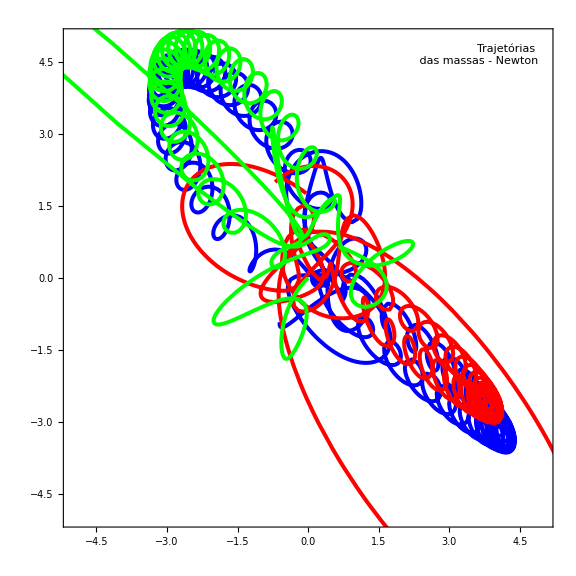

```mathematica
pltstyle={{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{Green,Thickness[0.005]}};
pltlegends={Style[Subscript["m"," 1"],FontSize->14,ScriptSizeMultipliers->.95],Style[Subscript["m"," 2"],FontSize->14,ScriptSizeMultipliers->.95],Style[Subscript["m"," 3"],FontSize->14,ScriptSizeMultipliers->.95]};

GN=1.0;
m1=1.0;
m2=1.0;
m3=1.0;
tmax=200.0;

vx10=0.93240737/2;
vy10=0.86473146/2;
vx20=0.93240737/2;
vy20=0.86473146/2;
vx30=-0.93240737;
vy30=-0.86473146;
x10=0.7;
y10=-0.5;
x20=-0.7;
y20=2.0;
x30=0.0;
y30=0.0;

ndsNewton=NDSolve[{x1'[t]==vx1[t],y1'[t]==vy1[t],x2'[t]==vx2[t],y2'[t]==vy2[t],x3'[t]==vx3[t],y3'[t]==vy3[t],m1 vx1'[t]==GN*(-((m1 m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-((m1 m3 (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))),m1 vy1'[t]==GN*(-((m1 m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-((m1 m3 (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))),m2 vx2'[t]==GN*(((m1 m2 (x1[t]-x2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-((m2 m3 (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2))),m2 vy2'[t]==GN*(((m1 m2 (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2))-((m2 m3 (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2))),m3 vx3'[t]==GN*(((m1 m3 (x1[t]-x3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+((m2 m3 (x2[t]-x3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2))),m3 vy3'[t]==GN*(((m1 m3 (y1[t]-y3[t]))/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2))+((m2 m3 (y2[t]-y3[t]))/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2))),x1[0]==x10,y1[0]==y10,x2[0]==x20,y2[0]==y20,x3[0]==x30,y3[0]==y30,vx1[0]==vx10,vy1[0]==vy10,vx2[0]==vx20,vy2[0]==vy20,vx3[0]==vx30,vy3[0]==vy30},{x1,x2,x3,y1,y2,y3,vx1,vx2,vx3,vy1,vy2,vy3},{t,0,tmax}];

plottabNewton={{x1[t],y1[t]},{x2[t],y2[t]},{x3[t],y3[t]}};

pltNewton=Legended[Show[Table[ParametricPlot[Evaluate[plottabNewton[[i]]/. ndsNewton],{t,0,tmax},PlotRange->{{-5,5},{-5,5}},Frame->True,PlotTheme->"Monochrome",PlotStyle->pltstyle[[i]],PlotLegends->Placed[{pltlegends[[i]]},{Left,Bottom}]],{i,1,3}],ImageSize->Large,BaseStyle->{FontFamily->"Times",14}],Placed[Style["Trajetórias \n das massas - Newton",Large],{{0.97,0.97},{1,1}}]];

(*Salvando na Área de Trabalho*)
desktopPath=Environment["USERPROFILE"]<>"\\Desktop\\";
Export[desktopPath<>"orbita_newton.png",pltNewton,ImageResolution->300];
pltNewton
```